# HW zero Name: Dhruvit Manojkumar Mavani

## 3) Import matrix

```mathematica
A = Import["https://math.nist.gov/pub/MatrixMarket2/Harwell-Boeing/gemat/gemat12.mtx.gz"]
```

SparseArray[…]

1)  Plotting of matrix A and finding eigenvalues

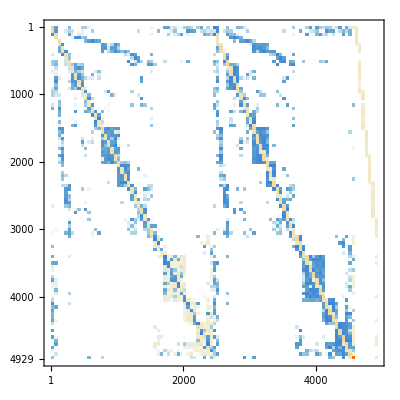

```mathematica
MatrixPlot[A]
```

```mathematica
Eigenvalues[A]
```

Eigenvalues::arh: Because finding 4929 out of the 4929 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

{-5.53063+0. ⅈ,5.2894+1.20544 ⅈ,5.2894-1.20544 ⅈ,0.519383+5.32119 ⅈ,0.519383-5.32119 ⅈ,4919,0.00604518+0. ⅈ,-0.0000832872+0.00293541 ⅈ,-0.0000832872-0.00293541 ⅈ,0.00259864+0. ⅈ,0.000315571+0. ⅈ}
 |  |  |  |